```mathematica
ClearAll["Global`*"];
```

```mathematica
r[t_]:=(x=-Sin[t];y=Cos[t];{x,y});
h[x_,y_,t_]:=(P1=r[2Pi*g[t]];P2=r[2Pi*g[f[t]]];(y-P1[[2]])*(P2[[1]]-P1[[1]])-(x-P1[[1]])*(P2[[2]]-P1[[2]]));
hd[t_]:=D[h[x_,y_,t],t];
(*Print[FullSimplify[h[x_,y_,t_]]];*)
(*Print[FullSimplify[hd[t_]]];*)
```

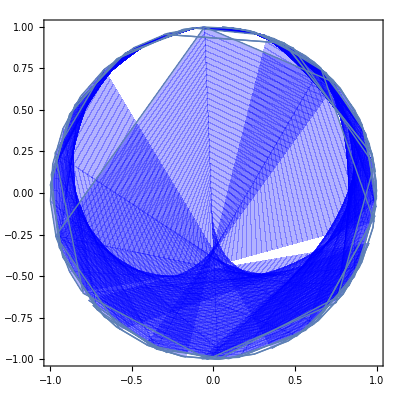

```mathematica
f[x_]:=x*4;
g[x_]:=x/2^Floor[Log[x]];
parametricFunc[t_,u_]:=(P1=r[2Pi*g[t]];P2=r[2Pi*g[f[t]]];{P1[[1]]+u*(P2[[1]]-P1[[1]]),P1[[2]]+u*(P2[[2]]-P1[[2]])});
ParametricPlot[parametricFunc[t,u],{t,0.01,1},{u,0,1},PlotStyle->Blue]
h[x_,y_,t_]:=(P1=r[2Pi*g[t]];P2=r[2Pi*g[f[t]]];(y-P1[[2]])*(P2[[1]]-P1[[1]])-(x-P1[[1]])*(P2[[2]]-P1[[2]]));
hd[t_]:=D[h[x_,y_,t],t];
(*Print[FullSimplify[h[x_,y_,t_]]];*)
(*Print[FullSimplify[hd[t_]]];*)
```

```mathematica
g[x_]:=x/2^((Log[x]-SawtoothWave[Log[x]]));
parametricFunc[t_,u_]:=(P1=r[2Pi*g[t]];P2=r[2Pi*g[f[t]]];{P1[[1]]+u*(P2[[1]]-P1[[1]]),P1[[2]]+u*(P2[[2]]-P1[[2]])});
ParametricPlot[parametricFunc[t,u],{t,0.01,1},{u,0,1},PlotStyle->Blue]
h[x_,y_,t_]:=(P1=r[2Pi*g[t]];P2=r[2Pi*g[f[t]]];(y-P1[[2]])*(P2[[1]]-P1[[1]])-(x-P1[[1]])*(P2[[2]]-P1[[2]]));
hd[t_]:=D[h[x_,y_,t],t];
(*Print[FullSimplify[hd[t_]]];*)
```

-Graphics-